```mathematica
hourlyBostonTemperatureTimeSeriesResample=TimeSeriesResample[WeatherData["KBOS","Temperature",{{2012,9,1},{2019,6,31}}],"Hour"]
```

TimeSeries[…]

```mathematica
RegularlySampledQ[%]
```

True

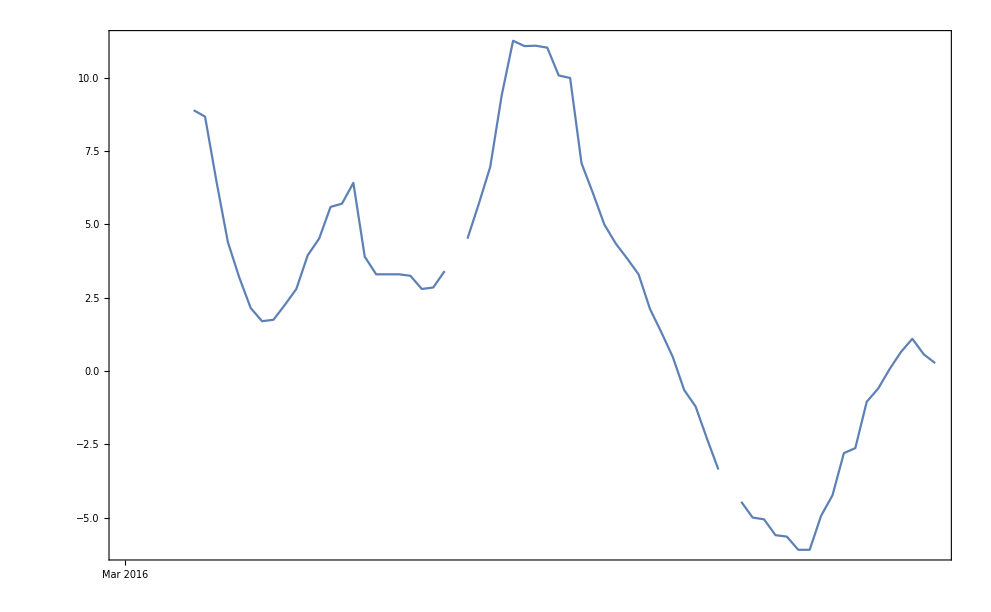

```mathematica
DateListPlot[TimeSeriesWindow[hourlyBostonTemperatureTimeSeriesResample,{DateObject[{2016,3,1}],DateObject[{2016,3,3}]}]]
```

```mathematica
SynthesizeMissingValues[Dataset@AssociationThread[hourlyBostonTemperatureTimeSeriesHasMissing["Dates"]->hourlyBostonTemperatureTimeSeriesHasMissing["Values"]]]
```

SynthesizeMissingValues::mlinclgth: Incompatible lengths: all features should contain the same number of examples.

SynthesizeMissingValues[Dataset[<>]]

```mathematica
18.9+0.9818181818181818 (-18.9+Missing["NotAvailable"])
```